hi

{{0,1.2},{0.3,2}}

hi

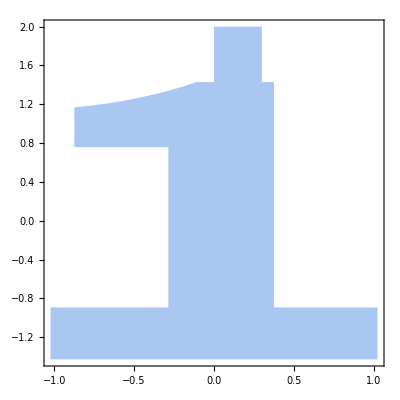
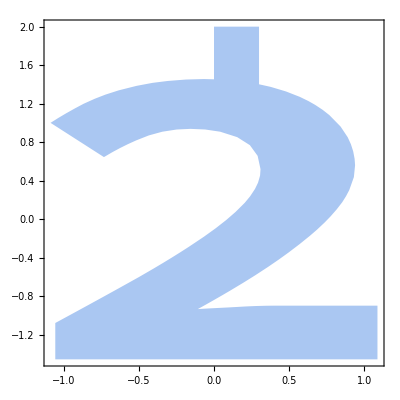
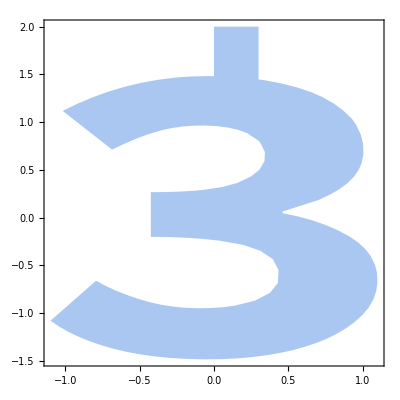
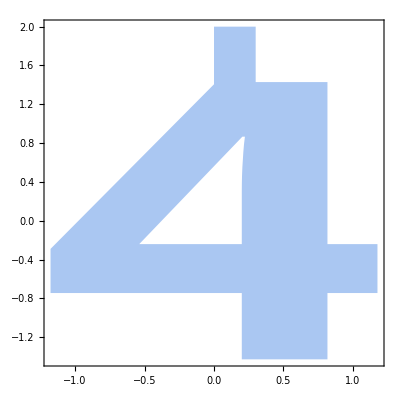
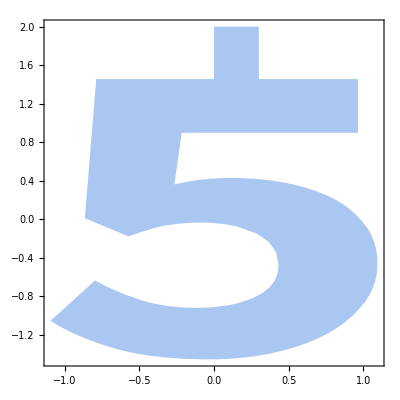
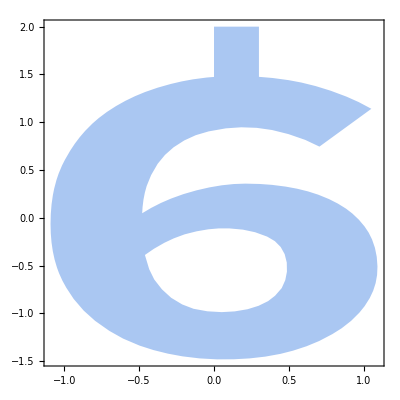
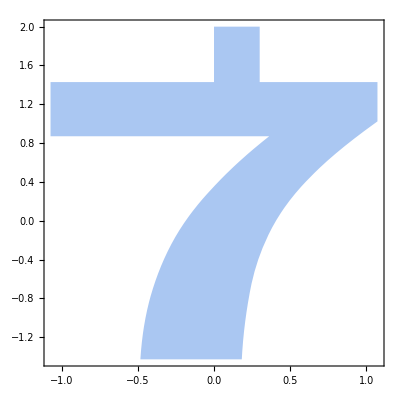
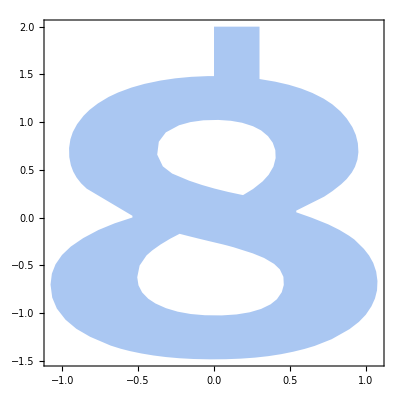

/home/anthony/Documents/Hedi/Swarm

matrixFEM/stiffness 0.mtx

matrixFEM/damping 0.mtx

```mathematica
Print["hi"]
Needs["NDSolve`FEM`"]

inletPosition={{0,1.2},{0.3,2}} (*this gives the dimensions of the inlet*)

Print["hi"]

inlet=Rectangle@@inletPosition;
arenaList=Table[
t=Text[Style[char,Bold]];

Ω=RegionUnion[inlet,#]&@TransformedRegion[#,0.5*{(Indexed[#,1]+0),(Indexed[#,2]+0)}&]&@BoundaryDiscretizeGraphics[t,_Text,MaxCellMeasure->0.03,PlotRange->All],
{char,ToString/@Range@9}];

Region[#,AspectRatio->1,Frame->True]&@
RegionUnion[inlet,#]&/@arenaList

t0=AbsoluteTime[];

index=6;

listofIndex={1,3};
Ω=arenaList[[index]];

nr=ToElementMesh[#,MaxCellMeasure->.001]&@BoundaryDiscretizeRegion@Ω;

vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[2]}},"DampingCoefficients"->{{1}}};
initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
SetDirectory@NotebookDirectory[]
Export["matrixFEM/stiffness 0.mtx",stiffness]
Export["matrixFEM/damping 0.mtx",damping]
```

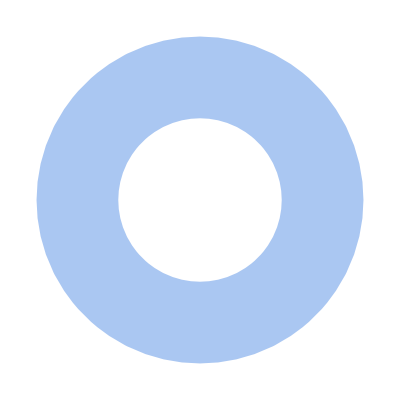

```mathematica
ring= RegionDifference[Disk[{0,0}, ToExpression["1"]],Disk[{0,0},0.5]]//Region
```

```mathematica
ring // Region
```

Region[…]

```mathematica
nr=ToElementMesh[#,MaxCellMeasure->.01]&@ring
```

ElementMesh[{{-1.,1.},{-1.,1.}},{TriangleElement[<348>]}]

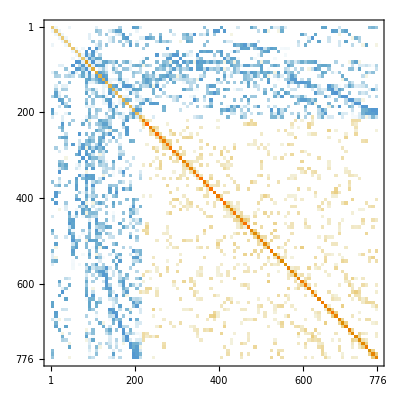

```mathematica
vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[2]}},"DampingCoefficients"->{{1}}};
initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

MatrixPlot@damping
```